```mathematica
ClearAll[ϖ];
ϖ[δ1_,δ2_,k_]:=ϖ[δ1,δ2,k]=If[k==δ1+δ2,1,Sum[ϖ[δ1,0,i]ϖ[0,δ2,k-i-1],{i,δ1,k-δ2}]]
```

```mathematica
ϖ[0,0,1]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of If[-510==-511+0,1,∑_(i=-511)^(-510-0) ϖ[-511-1,0,i] ϖ[0,0-1,-510-i-1]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of If[-509==-511+0,1,∑_(i=-511)^(-509-0) ϖ[-511-1,0,i] ϖ[0,0-1,-509-i-1]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[ϖ[-510-1,0,i] ϖ[0,0-1,-509-i-1]].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$Aborted

```mathematica
Table[ϖ[δ,0,k],{k,0,1},{δ,0,0}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 3-0.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[3-0].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1+Hold[Hold[3-0]].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$Aborted

```mathematica
ClearAll[c];
c[0,0]:=1;
c[δ_,i_]:=c[δ,i]=If[
δ==0,
c[1,i-1],
Max@Table[
With[{δ2=δ-δ1-1},
Sum[c[δ1,j]c[δ2,i-j],{j,0,i}]],
{δ1,0,δ-1}]]
```

```mathematica
Table[c[k,0],{k,1,10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[c[k,1],{k,1,10}]
```

{2,3,4,5,6,7,8,9,10,11}

```mathematica
Table[c[k,2],{k,1,10}]
```

{5,9,14,20,27,35,44,54,65,77}

```mathematica
Table[c[k,3],{k,1,10}]
```

{14,28,48,75,110,154,208,273,350,440}

```mathematica
Table[c[k,4],{k,1,10}]
```

{42,90,165,275,429,637,910,1260,1700,2244}

```mathematica
Table[c[2k,k],{k,1,10}]
```

{3,20,154,1260,10659,92092,807300,7152444,63882940,574221648}

```mathematica
Table[c[1,k],{k,1,10}]
```

{2,5,14,42,132,429,1430,4862,16796,58786}

```mathematica
Array[CatalanNumber,10]
```

{1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
Table[2/(i+2)Binomial[2i+1,i],{i,10}]
```

{2,5,14,42,132,429,1430,4862,16796,58786}

```mathematica
β n Log[β n/E]-n Log[n/E]-(β-1)n Log[(β-1)n/E]//Simplify
```

n (-Log[n]-(-1+β) Log[n (-1+β)]+β Log[n β])

```mathematica
β n Log[β n/E]-n Log[n/E]-(β-1)n Log[(β-1)n/E]/.β->6//Simplify
```

n Log[46656/3125]

```mathematica
β^β/(β-1)^(β-1)/.β->2
```

4

```mathematica
asymptoticBinomial[β_ n_,n_]:=(β^β/(β-1)^(β-1))^n √(β/(2π(β-1)n))
```

```mathematica
asymptoticBinomial[2n,n]
```

(4^n √(1/n))/(√π)

```mathematica
asymptoticBinomial[(α+2)i,i]//FullSimplify
```

((1+α)^(-1-α) (2+α)^(2+α))^i √((2+α)/(2 i π+2 i π α))

```mathematica
Assuming[α>0,Limit[(((1+α)^(-1-α) (2+α)^(2+α))^i )^(1/((α+1)i)),i->∞]]
```

(2+α)^((2+α)/(1+α))/(1+α)

```mathematica
((2+α)^((2+α)/(1+α))/(1+α)/.α->1/ϕ-1)//Simplify
```

(1+1/ϕ)^ϕ (1+ϕ)

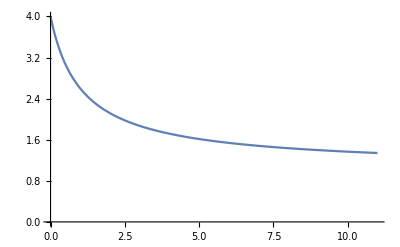

```mathematica
Plot[(2+α)^((2+α)/(1+α))/(1+α),{α,0,11},PlotRange->{0,4}]
```

```mathematica
Plot[(2+α)^((2+α)/(1+α))/(1+α),{α,0,11},PlotRange->{0,4}]
```

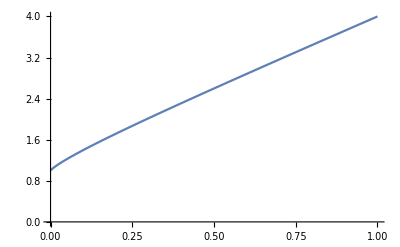

```mathematica
Plot[(1+1/ϕ)^ϕ (1+ϕ),{ϕ,0,1},PlotRange->{0,4}]
```